```mathematica
NotebookDirectory[]//SetDirectory;
```

```mathematica
<<"crediblePlot.m";
```

## Recoil Spectrum

```mathematica
dRdE=Import["DS_XENON_dRdE.dat"];
```

```mathematica
dRdE[[1;;6]]//MatrixForm
```

({//recoil,spectrum,for,detector,XENON}
{//WIMP,pars:,Mx,=,50,GeV,,spin,=,0.5,,C1,=,0.0001,,C2,=,0,,C3,=,0,,C4,=,0,,C5,=,0,,C6,=,0,,C7,=,0,,C8,=,0,,C9,=,0,,C10,=,0,,C11,=,0,,C12,=,0,,C13,=,0,,C14,=,0,,C15,=,0,}
{//,Astrophysical,parameters:,rho,=,0.3,GeV/cm^3,,v0,=,220,km/s,,vesc,=,544,km/s}
{//Er(keV),WIMP-rate,Bg-rate,total-rate,(/keV/t/year)})

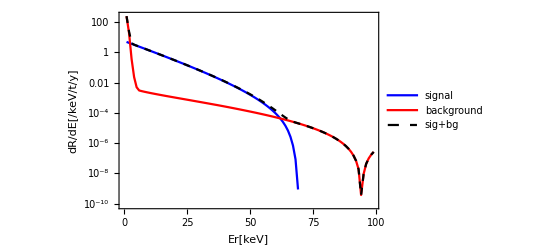

```mathematica
ListLogPlot[{dRdE⟦7;;All,{1,2}⟧,dRdE⟦5;;All,{1,3}⟧,dRdE⟦5;;All,{1,4}⟧},Joined->True,Frame->True,FrameStyle->Large,PlotStyle->{Blue,Red,{Black,Dashed}},FrameLabel->{"Er[keV]","dR/dE[/keV/t/y]"},PlotLegends->{"signal","background","sig+bg"},ImageSize->Large]
```

## Monte-Carlo Simulations

#### Spin Independent Simulation in Xenon

```mathematica
dataMC=Import["DS_sim.dat"];
```

```mathematica
dataMC[[1;;8]]//MatrixForm
```

({//,Asimov,simulation}
{//,WIMP,sim.,pars:,spin-0.5,,Mx,=,100}
{//,C1p,=,0.0001,,C2p,=,0,,C3p,=,0,,C4p,=,0,,C5p,=,0,,C6p,=,0,,C7p,=,0,,C8p,=,0,,C9p,=,0,,C10p,=,0,,C11p,=,0,,C12p,=,0,,C13p,=,0,,C14p,=,0,,C15p,=,0,}
{//,C1n,=,0.0001,,C2n,=,0,,C3n,=,0,,C4n,=,0,,C5n,=,0,,C6n,=,0,,C7n,=,0,,C8n,=,0,,C9n,=,0,,C10n,=,0,,C11n,=,0,,C12n,=,0,,C13n,=,0,,C14n,=,0,,C15n,=,0,}
{//Astrophysical,parameters:,rho,=,0.3,GeV/cm^3,,v0,=,220,km/s,,vesc,=,544,km/s}
{//,Detectors,used:}
{//,XENON,-,1,t.y,,nEvents,=,133.682}
{//,P,-2Log(L),Mx,C1n,rho,v0,vesc,vEp,vSp,C15p,C15n,C14p,C14n,C13p,C13n,C12p,C12n,C11p,C11n,C10p,C10n,C9p,C9n,C8p,C8n,C7p,C7n,C6p,C6n,C5p,C5n,C4p,C4n,C3p,C3n,C2p,C2n,C1p})

1 and 2σ marginalized credible regions in the mass vs coupling plane:

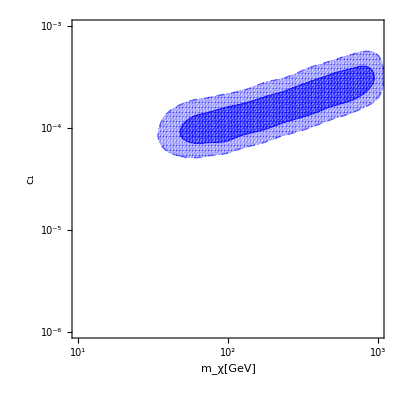

```mathematica
LogLogCrediblePlot2D[dataMC[[9;;All,{3,4,1}]],40,PlotRange->{{1,3},{-6,-3}},FrameLabel->{"m_χ[GeV]","c_1"}]
```

1D marginalized posterior for mass

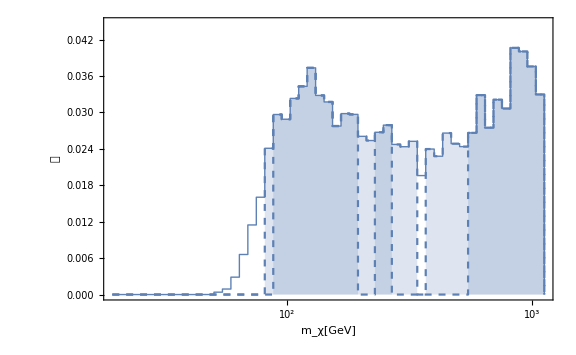

```mathematica
LogCrediblePlot1D[dataMC[[9;;All,{3,1}]],50,FrameLabel->{"m_χ[GeV]","𝒫"}]
```

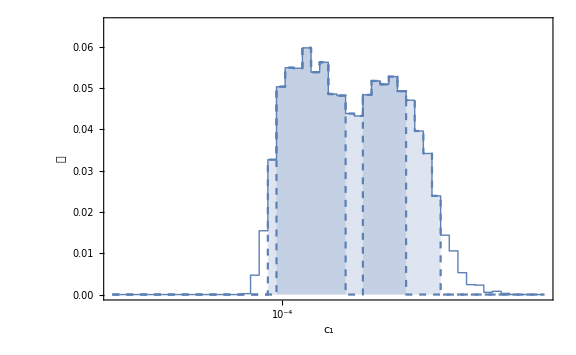

```mathematica
LogCrediblePlot1D[dataMC[[9;;All,{4,1}]],50,FrameLabel->{"c_1","𝒫"}]
```

## Evidence comparison

```mathematica
Import["evidence20.dat"]
```

Import::nffil: File not found during Import.

$Failed